```mathematica
NetInitialize[NetChain[{LinearLayer[1]},"Input"->1]]
```

NetChain[<>]

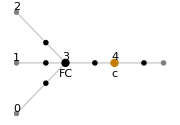

{NetChain[<>],-1.34807,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{
net=NetInitialize[NetChain[{LinearLayer[1]},"Input"->1]],
net[1]//First,
NetInformation[net,"MXNetNodeGraphPlot"],
NetInformation[net,"SummaryGraphic"],
NetInformation[net,"LayersGraph"]
}
```

```mathematica
ClassifierMeasurementsObject[net]
```

ClassifierMeasurementsObject[NetChain[<>]]

```mathematica
tune[#, 1]&/@Range[0,1,0.01]//ListAnimate
```

```mathematica
NetTrain[datum]
```

```mathematica
haha
```

```mathematica
NetExtract[net,{All,"Weights"}]
```

{{{-1.52473}}}

```mathematica
params=NetExtract[net,{{All,"Weights"},{All,"Biases"}}]//Flatten
```

```mathematica
{1.1630795001983643,-3.830782413482666}
```

```mathematica
haha
```

```mathematica
net[1]
```

{-1.52473}

```mathematica
format[{x_,y_}]:={x}->{y};
```

```mathematica
format/@datum
```

{{6.1101}→{17.592},{5.5277}→{9.1302},{8.5186}→{13.662},{7.0032}→{11.854},{5.8598}→{6.8233},{8.3829}→{11.886},{7.4764}→{4.3483},{8.5781}→{12},{6.4862}→{6.5987},{5.0546}→{3.8166},{5.7107}→{3.2522},{14.164}→{15.505},{5.734}→{3.1551},{8.4084}→{7.2258},{5.6407}→{0.71618},{5.3794}→{3.5129},{6.3654}→{5.3048},{5.1301}→{0.56077},{6.4296}→{3.6518},{7.0708}→{5.3893},{6.1891}→{3.1386},{20.27}→{21.767},{5.4901}→{4.263},{6.3261}→{5.1875},{5.5649}→{3.0825},{18.945}→{22.638},{12.828}→{13.501},{10.957}→{7.0467},{13.176}→{14.692},{22.203}→{24.147},{5.2524}→{-1.22},{6.5894}→{5.9966},{9.2482}→{12.134},{5.8918}→{1.8495},{8.2111}→{6.5426},{7.9334}→{4.5623},{8.0959}→{4.1164},{5.6063}→{3.3928},{12.836}→{10.117},{6.3534}→{5.4974},{5.4069}→{0.55657},{6.8825}→{3.9115},{11.708}→{5.3854},{5.7737}→{2.4406},{7.8247}→{6.7318},{7.0931}→{1.0463},{5.0702}→{5.1337},{5.8014}→{1.844},{11.7}→{8.0043},{5.5416}→{1.0179},{7.5402}→{6.7504},{5.3077}→{1.8396},{7.4239}→{4.2885},{7.6031}→{4.9981},{6.3328}→{1.4233},{6.3589}→{-1.4211},{6.2742}→{2.4756},{5.6397}→{4.6042},{9.3102}→{3.9624},{9.4536}→{5.4141},{8.8254}→{5.1694},{5.1793}→{-0.74279},{21.279}→{17.929},{14.908}→{12.054},{18.959}→{17.054},{7.2182}→{4.8852},{8.2951}→{5.7442},{10.236}→{7.7754},{5.4994}→{1.0173},{20.341}→{20.992},{10.136}→{6.6799},{7.3345}→{4.0259},{6.0062}→{1.2784},{7.2259}→{3.3411},{5.0269}→{-2.6807},{6.5479}→{0.29678},{7.5386}→{3.8845},{5.0365}→{5.7014},{10.274}→{6.7526},{5.1077}→{2.0576},{5.7292}→{0.47953},{5.1884}→{0.20421},{6.3557}→{0.67861},{9.7687}→{7.5435},{6.5159}→{5.3436},{8.5172}→{4.2415},{9.1802}→{6.7981},{6.002}→{0.92695},{5.5204}→{0.152},{5.0594}→{2.8214},{5.7077}→{1.8451},{7.6366}→{4.2959},{5.8707}→{7.2029},{5.3054}→{1.9869},{8.2934}→{0.14454},{13.394}→{9.0551},{5.4369}→{0.61705}}

```mathematica
model=NetTrain[net,format/@datum];
params=NetExtract[model,{{All,"Weights"},{All,"Biases"}}]//Flatten;
```

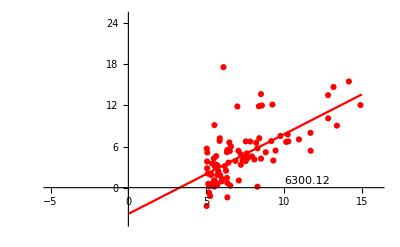

```mathematica
tune@@params
```

```mathematica
haha
```

```mathematica
tune@@params
```

-Graphics-